Thought on Stephen Wolfram’s idea of Computational Essay

```mathematica
Hyperlink["Computational Essay", "http://blog.stephenwolfram.com/2017/11/what-is-a-computational-essay/#more-14921"]
```

Compared to the two methods to insert a hyperlink in Mathematica, I prefer the way provided by Jupyter Notebook. Since the latter implement in a quiet intuitive way. I write down all the necessary attribute without clicking a mouse. But Wolfram give their explanation for this.

“The Wolfram Language underpins our technology stack, creating one cohesive process.Our notebooks offer a complete production environment from data import, prototyping, manipulation and testing which can all be done in the same notebook as deploying to the cloud or generating final reports or presentations.It doesn't need to be bundled with separate tools in the same way that iPython notebooks need to be, making our notebooks are better suited for computational essays since you don' t need to set up your notebook to use particular libraries.On top of that, since our language unifies our tech stack, there' s no issue with mutually incompatible interpreters like with Python, and even when you move to Jupyter which can take on multiple language kernels, it becomes increasingly difficult to ensure you have every needed package for each particular language.Markdown is useful in a notebook, but Markdown in iPython notebooks aren' t collapsible and that makes them difficult to structure.One additional key feature is our built - in knowledge base.Across thousands of domains, the Knowledgebase contains carefully curated expert knowledge directly derived from primary sources.It includes not only trillions of data elements, but also immense numbers of algorithms encapsulating the methods and models of almost every field.”

For me, The reasons Wolfram provided, the disadvantage of Jupyter notebook, is not  very satisfying. “... , since our languages unifies our tech stack, there’s no issue with mutually incompatible like with Python, and even when you move to Jupyter  which can take on multiple language kernels, it becomes increasingly difficult to ensure you have every needed package for each particular language.  I think set  virtual environment for each project already solved this program. I may love you more when Wolfram Language become a open source project, every one is accessible to the source code that put up this whole framework. 
Of course, what I thought is a problem doesn’t matter to the people who only care for getting the result. I think they would like to use magic if that’s possible. Even Kip Thorne, the master in GR, said “In practice I always did an implementation of the equation myself in Mathematica. I’m a real klutz computationally so Mathematica is just ideal for me.”
So many years, Wolfram accumulated enough resource.   I don’t know what to say about it.

```mathematica
Hyperlink["Kip Thorne with Mathematica","http://www.wolfram.com/mathematica/customer-stories/academy-award-visuals-mathematica-wolfram-language.en.html"]
```

```mathematica
Hyperlink[Plot[x Sin[1/x],{x,-.4,.4}],None]
```

```mathematica
EntityValue[RandomSample[LinguisticAssistant["NotableArtworks"], 10], "Image"]
```

Practice : Reproduce the command above.

```mathematica
FullForm[EntityValue[RandomSample[LinguisticAssistant["NotableArtworks"], 10], "Image"]]
```

“A New Form of Student Work   Computational essays are great for students to read, but they' re also great for students to write. Most of the current modalities for student work are remarkably old.Write an essay.Give a math derivation.These have been around for millennia.Not that there' s anything wrong with them.But now there' s something new : write a computational essay.And it' s wonderfully educational.

A computational essay is in effect an intellectual story told through a collaboration between a human author and a computer.The computer acts like a kind of intellectual exoskeleton, letting you immediately marshall vast computational power and knowledge.But it' s also an enforcer of understanding.Because to guide the computer through the story you' re trying to tell, you have to understand it yourself.

When students write ordinary essays, they' re typically writing about content that in some sense "already exists" ("discuss this passage"; "explain this piece of history"; …).But in doing computation (at least with the Wolfram Language) it' s so easy to discover new things that computational essays will end up with an essentially inexhaustible supply of new content, that' s never been seen before.Students will be exploring and discovering as well as understanding and explaining.

When you write a computational essay, the code in your computational essay has to produce results that fit with the story you' re telling. It' s not like you' re doing a mathematical derivation, and then some teacher tells you you've got the wrong answer.You can immediately see what your code does, and whether it fits with the story you' re telling.If it doesn't, well then maybe your code is wrong—or maybe your story is wrong.”

Teacher Gao holds the idea against mine of displaying the whole detail and procedure in one notebook. He argued that it makes too much  redundancy, and leaves the author more work to do in order to make it more readable.

```mathematica
W^μ==c +d
```

W^μ==c+d

```mathematica
Solve[{x+y==27,x y==180},{x,y}]
```

{{x→12,y→15},{x→15,y→12}}

```mathematica
Solve[{x+y==3, x y ==111},{x,y}]
```

{{x→1/2 (3-ⅈ √435),y→1/2 (3+ⅈ √435)},{x→1/2 (3+ⅈ √435),y→1/2 (3-ⅈ √435)}}

```mathematica
w^μ=a+b
```

Set::write: Tag Power in w^μ is Protected.

2 b+c

```mathematica
FullForm[W^μ]
```

Power[W,\[Mu]]

```mathematica
?MatrixQ
```

MatrixQ[expr] gives True if expr is a list of lists or a two-dimensional SparseArray object that can represent a matrix, and gives False otherwise. 
MatrixQ[expr,test] gives True only if test yields True when applied to each of the matrix elements in expr.

```mathematica
H={{0},{v}}
```

(0
v)

```mathematica
(*Define a list*)
```

```mathematica
Remove[τ]
```

```mathematica
τ=List[τ1, τ2, τ3]
τ1=1/2{{0,1},{1,0}}
τ2=1/2{{0,-I},{I,0}}
τ3=1/2{{1,0},{0,-1}}
MatrixForm[τ]
```

{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}

{{0,1/2},{1/2,0}}

{{0,-ⅈ/2},{ⅈ/2,0}}

{{1/2,0},{0,-1/2}}

((0
1/2) | (1/2
0)
(0
-ⅈ/2) | (ⅈ/2
0)
(1/2
0) | (0
-1/2))

```mathematica
FullForm[τ]
```

List[\[Tau]1,\[Tau]2,\[Tau]3]

```mathematica
τ[[1]]
```

τ1

```mathematica
τ = {1, 2}
```

{1,2}

```mathematica
(*Access an element from it*)
```

```mathematica
τ[1]
```

{1,2}[1]

```mathematica
τ1=1/2{{0,1},{1,0}}
```

{{0,1/2},{1/2,0}}

```mathematica
τ2=1/2{{0,-I},{I,0}}
```

{{0,-ⅈ/2},{ⅈ/2,0}}//.MatrixForm

```mathematica
τ3=1/2{{1,0},{0,-1}}
```

{{1/2,0},{0,-1/2}}

```mathematica
τ
```

{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}

```mathematica
MatrixForm[τ]
```

({{0,1/2},{1/2,0}}
{{0,-ⅈ/2},{ⅈ/2,0}}//.MatrixForm
{{1/2,0},{0,-1/2}})

```mathematica
1/Sqrt[2](τ1+I τ2)
```

(0 | 1/(√2)
0 | 0)

```mathematica
co[a_,b_]:=Dot[ a ,b] - Dot[b ,a]
```

```mathematica
W[μ_,ν_]:= Dot[W_μ, W_ν]-Dot[W
```

```mathematica
Quit
```

```mathematica
Import["/home/wm/Projects/feyncalc/FeynCalc/Dirac/DiracEquation.m"]
```

Global`DiracEquation`Private`

```mathematica
∑_(index=start)^end expr
```

```mathematica
?DiracEquation
```

DiracEquation[exp] applies the Dirac equation without expanding exp. If that is needed, use DiracSimplify.

```mathematica
?MTD
```

Information::notfound: Symbol MTD not found.

```mathematica
URL["https://reference.wolfram.com/workbench/index.jsp?topic=/com.wolfram.eclipse.help/html/tasks/code.html"]
```

URL[https://reference.wolfram.com/workbench/index.jsp?topic=/com.wolfram.eclipse.help/html/tasks/code.html]

As a new hand in TP, "If you don't feel thrilled by what the fundamental questions, therefore, the reason is you didn't comprehend physics in it. All you learned is absurd tricks in computation"

I will demonstrate how to do symbolic computation in Mathematica, with elegant  programming  design .

#### Thought road

I  want to calculate  with tensor, a variable with upper and lower index.m
There  is already way to solve my problem,  FeynCalc, MathGR, etc. But I don’t know how to learn from their source code. How  to imitate their programming style.
I am always given a formula.

```mathematica
Subscript[Γ, μν]^κ:= 1/2 g^κλ((∂Subscript[g, μλ])/(∂x^ν)+(∂Subscript[g, νλ])/(∂x^μ)-(∂Subscript[g, μν])/(∂x^λ))
```

Derivative::novar: ∂g_μλ cannot be interpreted. A partial derivative requires a subscript differentiation variable.

```mathematica
Subscript[Γ, μν]^κ:= 1/2 g^κλ(D[Subscript[g, μλ],x^ν]+D[Subscript[g, νλ],x^ν]-D[Subscript[g, μν],x^λ])
```

SetDelayed::write: Tag Power in Γ_μν^κ is Protected.

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n.
D[f,x,y,…] gives the partial derivative ⋯ (∂/∂y)(∂/∂x) f.
D[f,{x,n},{y,m},…] gives the multiple partial derivative ⋯ (∂^m /∂y^m)(∂^n /∂x^n) f.
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives an array derivative.

```mathematica
FullForm[Subscript[Γ, μν]^κ]
```

Power[Subscript[\[CapitalGamma],\[Mu]\[Nu]],\[Kappa]]

```mathematica
Sin[Pi]
```

0

```mathematica
?Subscript
```

Subscript[x,y] is an object that formats as x_y. 
Subscript[x,y_1,y_2,…] formats as x_(y_1,y_2,…).

```mathematica
?FullForm
```

FullForm[expr] prints as the full form of expr, with no special syntax.

file.m is a Wolfram Language package file.

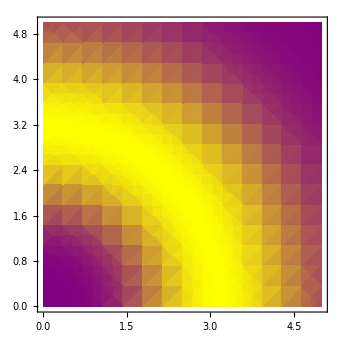

```mathematica
f[x_,y_]:=(x^2+y^2)^2 Exp[-((x^2+y^2)/5)]

DensityPlot[f[x,y],{x,0,5},{y,0,5},ColorFunction->(Blend[{Purple,Yellow},#]&)]
```